### Testing the Solution to the Fredholm Equation for m

1.

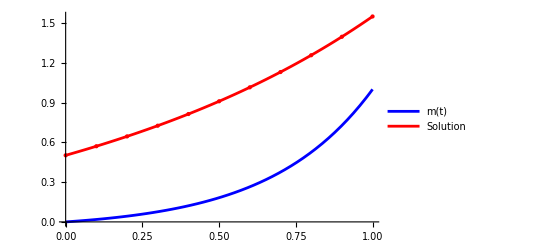

```mathematica
(*Define the parameters*)
n = 2;
rho = 1.0
alpha=rho (n+1)/(n-1);
m[t_]:=(Exp[alpha t]-1)/(Exp[alpha]-1);
mPrime[t_]:=D[m[t],t];

(*Define the Fredholm equation*)
fredholmEq[t_]:=n Integrate[Exp[-rho (t-s)] mPrime[s],{s,0,t}]+Integrate[Exp[-rho (u-t)] mPrime[u],{u,t,1}];

(*Evaluate the solution*)
solution[t_]:=FullSimplify[fredholmEq[t]]

(*Plot m(t) and the solution*)
Plot[{m[t],Evaluate[solution[t]]},{t,0,1},PlotStyle->{Blue,{Red,PointSize[0.02]}},PlotLegends->{"m(t)","Solution"},Epilog->{Red,PointSize[Large],Point[{#,solution[#]}]&/@Table[t,{t,0,1,0.1}]}]
```

```mathematica
(* Solve the differential equation for mPrime *)
```

```mathematica
(*Solve the differential equation for mPrime*)
solveFredholmEquation:=Module[{sol},sol=Solve[fredholmEq[t]==0,mPrime[t]]];

(*Plotting the solution*)
Module[{solution},solution=solveFredholmEquation;
Plot[{m[t],Evaluate[mPrime[t]/. solution]},{t,0,1},PlotStyle->{Blue,{Red,PointSize[0.02]}},PlotLegends->{"m(t)","m'(t)"},Epilog->{Red,PointSize[Large],Point[{#,(mPrime[#]/. solution)}]&/@Table[t,{t,0,1,0.1}]}]]
```

Solve::ivar: 0.157187 ⅇ^(3. t) is not a valid variable.

D::ivar: 0. is not a valid variable.

Solve::ivar: 0.157187 ⅇ^(3. t) is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

ReplaceAll::reps: {Solve[0.580732 ⅇ^t-0.0785935 ⅇ^(3. t)+2 (-0.0785935 Power[«2»]+0.0785935 Power[«2»])==0,0.157187 ⅇ^(3. t)]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

D::ivar: 0.1 is not a valid variable.

ReplaceAll::reps: {Solve[0.580732 ⅇ^t-0.0785935 ⅇ^(3. t)+2 (-0.0785935 Power[«2»]+0.0785935 Power[«2»])==0,0.157187 ⅇ^(3. t)]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

D::ivar: 0.2 is not a valid variable.

General::stop: Further output of D::ivar will be suppressed during this calculation.

ReplaceAll::reps: {Solve[0.580732 ⅇ^t-0.0785935 ⅇ^(3. t)+2 (-0.0785935 Power[«2»]+0.0785935 Power[«2»])==0,0.157187 ⅇ^(3. t)]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-